```mathematica
d={{1,1},{2,4},{5,1},{8,-4},{9,-3},{10,1},{11,1},{11.1,2},{11.4,4},{12,0}};
d={#[[2]],#[[1]]}&/@hedgeI[[1;;120]];dt=d;
n=Length[d]-1;(*Anzahl der Punkte - 1*)
p=10;(*Ordnung*)
m=n+1+p ;(*Anzahl der Knots - 1*)
(*Knot-Erzeugung*)
u=Join[Table[0,{i,p}],Table[i/(n+1-p),{i,0,n+1-p}],Table[1,{i,p}]];w=Table[1,{i,n+1}];
```

```mathematica
P[t0_]:=Module[{a,k,j=m,i,t=t0,u=u,d=d*w,p=p,n=n,m=m,w=w},
(*j Bestimmtung*)
If[t==0,j=1,
While[t<=u[[j]],j--]];
If[j<=p,j=p+1];

(*Gewichtung*)

(*Berechnung*)
For[k=1,k≤p,k++,
For[i=j-p+k,i≤j,i++,
a=(t-u[[i]])/(u[[i+p+1-k]]-u[[i]]);
d[[i]]=(1-a)d[[i-1]]+a d[[i]];
w[[i]]=(1-a)w[[i-1]]+a w[[i]];
];
];
d[[j]]/w[[j]]
]
```

```mathematica
w=(M[Length[d]].Transpose[d][[2]]);w=(0.01+w/Max[w])^2;
```

```mathematica
d={};c=10;AppendTo[d,dt[[1]]];
For[i=2,i<Length[dt],i++,
fs=(dt[[i+1,2]]-dt[[i-1,2]])/2 (n-1);
k=(-2dt[[i,2]]+dt[[i+1,2]]+dt[[i-1,2]])(n-1)^2/(1+fs^2)^(3/2);
AppendTo[d,dt[[i]]+{ArcTan[c k]/Pi/(n-1),0}];
]
AppendTo[d,dt[[Length[dt]]]];
```

```mathematica
tt=Table[P[x],{x,0,1,0.001}];
```

```mathematica
q=Total[1/n/Variance[Transpose[dt][[2]]](#[[2]]-IP[#[[1]]])^2&/@dt]
```

0.00690507

```mathematica
0.003453418910958665
```

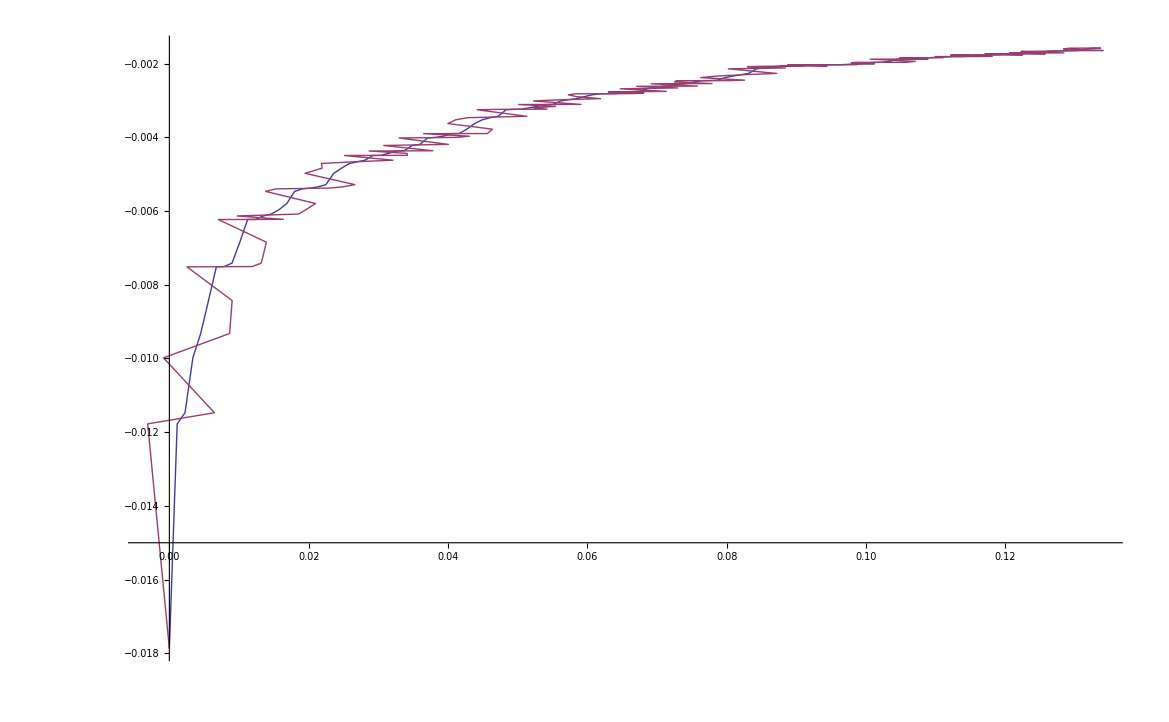

```mathematica
ListPlot[{dt,d},Joined->True,PlotRange->All]
```

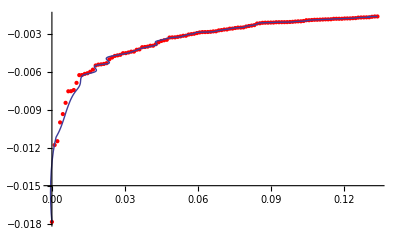

```mathematica
Show[ListPlot[dt,PlotStyle->Red,PlotRange->All],ListPlot[tt,Joined->True,PlotRange->All]]
```

```mathematica
Show[ListPlot[d,PlotStyle->Red,PlotRange->All],ListPlot[tt,Joined->False,PlotRange->All]]
```

```mathematica
ListPlot[{#[[1]],#[[2]]-IP[#[[1]]]}&/@d]
```

Part::partd: Part specification {{-0.0665223, 0.}, {-0.0576328, 0.00595448}, {-0.0520835, 0.012011}, « 5 », {-0.0348844, 0.0495703}, {-0.0331208, 0.0557423}, « 91 »} ⟦ 0, 1 ⟧ is longer than depth of object.

Part::partd: Part specification {{-0.0665223, 0.}, {-0.0576328, 0.00595448}, {-0.0520835, 0.012011}, « 5 », {-0.0348844, 0.0495703}, {-0.0331208, 0.0557423}, « 91 »} ⟦ 0, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

```mathematica
d[[350]]//N
```

{-0.00612564,0.392135}

```mathematica
IP[-0.006125639472671196]
```

0.394174

```mathematica
IP[t0_]:=Module[{t=t0,tt=tt,j=Length[tt]},
(*j Bestimmtung*)
If[t==0,j=1,
While[t≤tt[[j,1]],j--]];
tt[[j,2]]+(tt[[j+1,2]]-tt[[j,2]])(t-tt[[j,1]])/(tt[[j+1,1]]-tt[[j,1]])
]
```

```mathematica
M[n_]:=SparseArray[{{1,1}->-1,n{1,1}->1,{i_,j_}/;i==1&&i==j-1->1,{i_,j_}/;i==n&&i==j+1->-1,{i_,j_}/;i==j+1->-1/2,{i_,j_}/;i==j-1->1/2},n{1,1}];
```

```mathematica
Length[w]
```

119